Nonlonear system ODEs  (§12):

```mathematica
Quit[]
```

```mathematica
prey=n*(0.1-0.1*P)
pred=P*(-1+0.1*n)
```

n (0.1-0.1 P)

(-1+0.1 n) P

```mathematica
equil=Values[NSolve[{prey==0,pred==0},{n,P}]]
```

{{10.,1.},{0.,0.}}

```mathematica
jac=D[{prey,pred},{{n,P}}];
MatrixForm[jac]
```

(0.1-0.1 P | -0.1 n
0.1 P | -1+0.1 n)

```mathematica
jac1=jac/.{n->equil[[2,1]],P->equil[[2,2]]};
MatrixForm[jac1]
```

(0.1 | 0.
0. | -1.)

```mathematica
Eigenvalues[jac1]
```

{-1.,0.1}

```mathematica
Det[jac1]
```

-0.1

```mathematica
jac2=jac/.{n->equil[[1,1]],P->equil[[1,2]]};
MatrixForm[jac2]
Eigenvalues[jac2]
Det[jac2]
Tr[jac2]
```

(0. | -1.
0.1 | 0.)

{0.+0.316228 ⅈ,0.-0.316228 ⅈ}

0.1

0.

n'[t]==n[t] (0.1-0.1 P[t])

P'[t]==(-1+0.1 n[t]) P[t]

{n[0]==7,P[0]==1}

{InterpolatingFunction[{{0., 50.}}, <>][t],InterpolatingFunction[{{0., 50.}}, <>][t]}

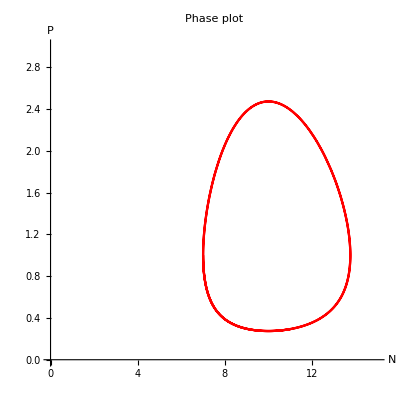

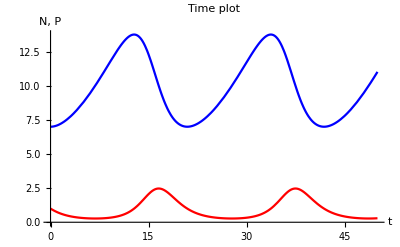

```mathematica
preydiff=D[n[t],t]==n[t]*(0.1-0.1*P[t])
preddiff=D[P[t],t]==P[t]*(-1+0.1*n[t])
sys={preydiff,preddiff};
init={n[0]==7,P[0]==1}
sol=NDSolveValue[{sys,init},{n[t],P[t]},{t,0,50}]
ParametricPlot[sol,{t,0,50},PlotRange->{{0,15},{0,3}},PlotStyle->Red,AspectRatio->1,PlotLabel->"Phase plot", AxesLabel->{"N","P"}]
Plot[sol,{t,0,50},PlotLabel->"Time plot",AxesLabel->{"t","N, P"},PlotStyle->{Blue,Red}]
```

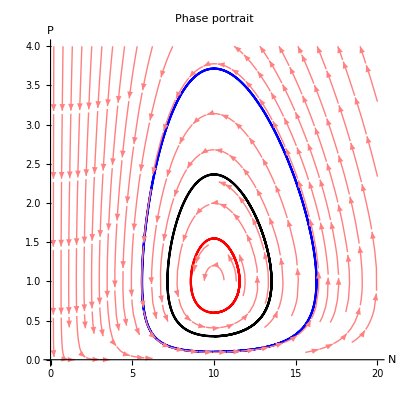

```mathematica
init1={n[0]==10,P[0]==0.1};
init2={n[0]==10,P[0]==0.3};
init3={n[0]==10,P[0]==0.6};
sol1=NDSolveValue[{sys,init1},{n[t],P[t]},{t,0,100}];
sol2=NDSolveValue[{sys,init2},{n[t],P[t]},{t,0,50}];
sol3=NDSolveValue[{sys,init3},{n[t],P[t]},{t,0,50}];
Show[ParametricPlot[{sol1,sol2,sol3},{t,0,50},PlotRange->{{0,20},{0,4}},PlotStyle->{Blue,Black,Red},AspectRatio->1,PlotLabel->"Phase portrait", AxesLabel->{"N","P"}],StreamPlot [{prey,pred},{n,0,20},{P,0,4},StreamScale->{Tiny,Automatic,0.02}, StreamStyle->Pink]]
```

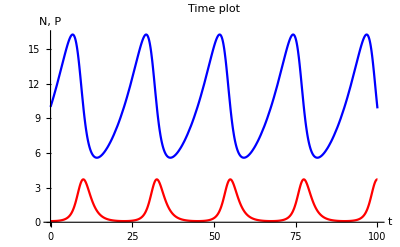

```mathematica
Plot[sol1,{t,0,100},PlotLabel->"Time plot",AxesLabel->{"t","N, P"},PlotStyle->{Blue,Red}]
```